```mathematica
Build::usage="Build@k gives the extended DT form of the knot k, which is given in modified DT form.";
Compactify::usage="Compactify@k gives the modified DT form of the knot k, which is given in extended DT form.";
Shift::usage="Shift[k, o, s] gives the result of shifting the knot k, which is given in modified DT form, by o units forward and reversing the direction if the sign s is negative.";
Minimal::usage="Minimal@k gives the lexicographically smallest indexing of the knot k, which is given in modified DT form.";
KnotGraph::usage="KnotGraph@k gives the modified 3-valent graph with 4 vertices in a square at each crossing of the knot k, which is given in modified DT form.";
KnotSort::usage="KnotSort@l sorts the knots of the list l where alternating knots always come first and all further order is determined lexicographically where non-alternating knots are first compared by absolute value, and then further canonically.";
PermutationConjugation::usage="PermutationConjugation[a, g] gives the conjugation of the permutations a and g by evaluating gag^-1";
Convert::usage="Convert@k gives the minimial modified DT form of the knot k, which is given in extended DT form.";
SortedQ::usage="SortedQ@l gives True if the list of knots l is sorted and False otherwise.";
PassMapping::usage="PassMapping[v, l, p, c, n, a, i] gives the values that a should be mapped to after a 2-pass has been made at index i, from indices v with all indices l, passing over the list of strands c, in an n-crossing knot with a list of pairs p.";
TwoPass::usage="TwoPass@k gives all the knots that can be obtained by applying one 2-pass to the knot k, which is given in modified DT form.";
ReidemeisterOne::usage="ReidemeisterOne@k gives all the knots that can be obtained by adding a positive kink at an even index to the knot k, which is given in modified DT form.";
ReidemeisterThree::usage="ReidemeisterThree@k gives all the knots that can be obtained by applying one third Reidemeister move to the knot k, which is given in modified DT form.";
Flype::usage="Flype@l gives a list of lists of all of the knots that can be obtained by applying one flype to each knot of the list l.";
PassReducible::usage="PassReducible@k gives True if the knot k, which is given in modified DT form, is reducible with a 2,1-pass move or a 3,2-pass move, and False otherwise.";
ReducibleQ::usage="ReducibleQ@k gives True if the knot k, which is given in modified DT form, can be reduced using the first Reidemeister move, a 2,1-pass move, or a 3,2-pass move and False otherwise.";
CandidateKnots::usage="CandidateKnots@n gives the sorted list of all irreducible planar minimal alternating knot diagrams with n crossings.";
AlternatingKnots::usage="AlternatingKnots@n gives the sorted list of all irreducible planar minimal alternating knots with n crossings.";
ValidKnots::usage="ValidKnots@n gives the sorted list of all non-trivially reducible planar minimal knot diagrams with n crossings.";
KnotAssociation::usage="KnotAssociation@n gives an association that returns the list of all valid knots with n crossings whose alternating form is equal to the given knot.";
Data::usage="Data@n gives the file that graphs of knots with n crossings will be saved to and loaded from.\nData@\"all\" gives the file that the graph of all knots with up to 10 crossings will be saved to and loaded from.";
GraphSort::usage="GraphSort@[a, b] returns True if the lists a and b, containing a pair of vertices and an edge name, are in sorted order and False otherwise.";
CreateGraph::usage="CreateGraph@n gives a graph with minimal irreducible knot diagrams with n crossings as vertices and edges connecting each pair of knot diagrams that are equivalent under one 2-pass, flype, or third Reidemeister move.\nCreateGraph@\"all\" gives a graph with minimal irreducible knot diagrams with up to 10 crossings as vertices and edges connecting each pair of knot diagrams that are equivalent under one 2-pass, flype, or third Reidemeister move.";
MakeGraph::usage="MakeGraph@n creates the graph of knot diagrams with n crossings and then saves it to the appropriate file.\nMakeGraph@\"all\" creates the graph of knot diagrams with up to 10 crossings and then saves it to the appropriate file.";
DrawGraph::usage="DrawGraph@n displays the graph of knot diagrams with n crossings that it loaded from the appropriate file.\nDrawGraph@\"all\" displays the graph of knot diagrams with up to 10 crossings.";
Strand::usage="Strand[i, j] represents a strand from index i to index j that can be stitched with other strands into longer strands or circles.";
ToPD::usage="ToPD@k gives a planar diagram notation for the knot k, which is given in modified DT form.";
Writhe::usage="Writhe@k gives the writhe, the difference between the number of right-handed and left-handed crossings, of the knot k, which is given in modified DT form.";
JonesPolynomial::usage="JonesPolynomial@k gives the Jones polynomial of the knot k, which is given in modified DT form.";
EdgeSequence::usage="EdgeSequence@k gives a list of the strands in the order that they should be calculated from the generators, which are returned as a list as the first element of the result, of the knot k, which is given in modified DT form.";
ValidColouring::usage="ValidColouring[k, e, s, g] gives True if the knot k, given in expanded planar diagram notation, can be coloured by edge generators, crossing mappings, and generator values given by the lists e, s, and g, respectively and False otherwise.";
Colourings::usage="Colourings[k, m] gives the number of colourings of the knot k, which is given in modified DT form onto the permutation group S_m.";
Invariants::usage="Invariants[a, t] gives the new values of a and t after one of each set of equivalent knots in a is moved to t.";
RolfsenTable::usage="RolfsenTable@n gives the set of knots in the Rolfsen table with n crossings.\nRolfsenTable[] produces the Rolfsen table, the table of knots with 10 crossings or fewer.";
```

```mathematica
?Build
```

Build@
StyleBox["k",
FontSlant->"Italic"] gives the extended DT form of the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
Build@k_MDT:=Build@k=EDT[2Range@Length@k-1,2List@@k];
```

```mathematica
?Compactify
```

Compactify@
StyleBox["k",
FontSlant->"Italic"] gives the modified DT form of the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in extended DT form.

```mathematica
Compactify@k_EDT:=Compactify@k=MDT@@(({1,Sign[#⟦1⟧#⟦2⟧]}
Mod[Abs@If[OddQ@#⟦1⟧,#,#⟦{2,1}⟧],2Length@k⟦1⟧,1]&
/@(List@@kᵀ)
//Sort)ᵀ⟦2⟧
//Sign@#⟦1⟧#/2&);
```

```mathematica
?Shift
```

Shift[
StyleBox["k",
FontSlant->"Italic"], 
StyleBox["o",
FontSlant->"Italic"], 
StyleBox["s",
FontSlant->"Italic"]] gives the result of shifting the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form, by 
StyleBox["o",
FontSlant->"Italic"] units forward and reversing the direction if the sign 
StyleBox["s",
FontSlant->"Italic"] is negative.

```mathematica
Shift[k_MDT,o_Integer,s_Integer]:=Compactify[EDT@@(Sign[List@@Build@k]
(o+Abs[List@@Build@k]s+2Length@k))];
```

```mathematica
?Minimal
```

Minimal@
StyleBox["k",
FontSlant->"Italic"] gives the lexicographically smallest indexing of the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
Minimal@k_MDT:=Minimal@k=(Array[Shift[k,#1,(-1)^#2]&,{2Length@k,2}]
//Join@@#&
//KnotSort)⟦1⟧;
```

```mathematica
?KnotGraph
```

KnotGraph@
StyleBox["k",
FontSlant->"Italic"] gives the modified 3-valent graph with 4 vertices in a square at each crossing of the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
KnotGraph@k_MDT:=KnotGraph@k=(Join@@Table[
Array[{v,#-1}<->{v,Mod[#,4]}&,4]∪
{{v,0}<->{Ordering[List@@Abs/@k]⟦v⟧,1},
{v,2}<->{Ordering[List@@Abs/@k]⟦Mod[v-1,Length@k,1]⟧,3}},
{v,Length@k}]//Graph);
```

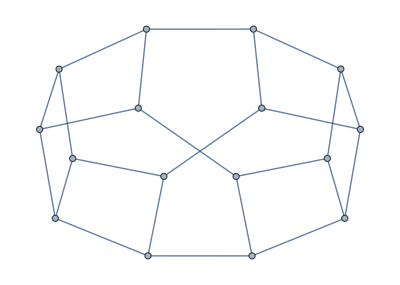

```mathematica
KnotGraph@MDT[2,3,4,1]
```

```mathematica
?KnotSort
```

KnotSort@
StyleBox["l",
FontSlant->"Italic"] sorts the knots of the list 
StyleBox["l",
FontSlant->"Italic"] where alternating knots always come first and all further order is determined lexicographically where non-alternating knots are first compared by absolute value, and then further canonically.

```mathematica
KnotSort@l_List:=KnotSort@l=Sort[l,If[Length@#1==Length@#2,
If[#1===Abs/@#1,#2=!=Abs/@#2||Order[#1,#2]==1,
#2=!=Abs/@#2&&If[Abs/@#1===Abs/@#2,Order[#1,#2]==1,
Order[Abs/@#1,Abs/@#2]==1]],
Length@#1<Length@#2]&];
```

```mathematica
KnotSort@{MDT[2,4,5,-7,1,8,9,-3,10,6],MDT[4,5,8,7,1,9,10,3,2,6],MDT[2,4,5,-7,1,-8,-9,-3,-10,-6],MDT[2,3,1]}
```

{MDT[2,3,1],MDT[4,5,8,7,1,9,10,3,2,6],MDT[2,4,5,-7,1,-8,-9,-3,-10,-6],MDT[2,4,5,-7,1,8,9,-3,10,6]}

```mathematica
?PermutationConjugation
```

PermutationConjugation[
StyleBox["a",
FontSlant->"Italic"], 
StyleBox["g",
FontSlant->"Italic"]] gives the conjugation of the permutations 
StyleBox["a",
FontSlant->"Italic"] and 
StyleBox["g",
FontSlant->"Italic"] by evaluating SuperscriptBox[
 StyleBox["gag",
FontSlant->"Italic"], 
 RowBox[{"-", "1"}]]

```mathematica
PermutationConjugation[a_List,g_List]:=PermutationConjugation[a,g]=
PermutationProduct[g,a,InversePermutation@g];
```

```mathematica
PermutationConjugation[{4,1,5,2,3},{3,5,4,1,2}]
```

{2,1,5,3,4}

```mathematica
?Convert
```

Convert@
StyleBox["k",
FontSlant->"Italic"] gives the minimial modified DT form of the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in extended DT form.

```mathematica
Convert@k_EDT:=Convert@k=Minimal@Compactify@k;
```

```mathematica
?SortedQ
```

SortedQ@
StyleBox["l",
FontSlant->"Italic"] gives True if the list of knots 
StyleBox["l",
FontSlant->"Italic"] is sorted and False otherwise.

```mathematica
SortedQ@l_List:=SortedQ@l=l===KnotSort@l;
```

```mathematica
?PassMapping
```

PassMapping[
StyleBox["v",
FontSlant->"Italic"], 
StyleBox["l",
FontSlant->"Italic"], 
StyleBox["p",
FontSlant->"Italic"], 
StyleBox["c",
FontSlant->"Italic"], 
StyleBox["n",
FontSlant->"Italic"], 
StyleBox["a",
FontSlant->"Italic"], 
StyleBox["i",
FontSlant->"Italic"]] gives the values that 
StyleBox["a",
FontSlant->"Italic"] should be mapped to after a 2-pass has been made at index 
StyleBox["i",
FontSlant->"Italic"], from indices 
StyleBox["v",
FontSlant->"Italic"] with all indices 
StyleBox["l",
FontSlant->"Italic"], passing over the list of strands 
StyleBox["c",
FontSlant->"Italic"], in an 
StyleBox["n",
FontSlant->"Italic"]-crossing knot with a list of pairs 
StyleBox["p",
FontSlant->"Italic"].

```mathematica
PassMapping[v_List,l_List,p_List,c_List,n_Integer,a_Integer,i_Integer]:=
PassMapping[v,l,p,c,n,a,i]=If[Length[v∩l⟦;;2⟧]==1,
Mod[If[MemberQ[v∪Join@@c,a],
If[MemberQ[c⟦1⟧,a],a+If[Mod[Abs@p⟦l⟦1⟧⟧-i,2n]>1,1,-1],
If[MemberQ[c⟦2⟧,a],a+If[Mod[Abs@p⟦l⟦3⟧⟧-i,2n]>1,1,-1],
(l⟦{2,1,4,3}⟧+{-1,1,-1,1})
⟦Position[l,If[OddQ[l⟦1⟧+l⟦2⟧],Total@v-a,a]]⟦1,1⟧⟧]],
a],2n,1]
If[MemberQ[v∪Join@@c,a]||EvenQ@a,
If[Mod[a-i,2n]≤1||OddQ@a&&¬MemberQ[l,a],-Sign@p⟦a⟧,1],
Sign@p⟦a⟧],
Mod[If[MemberQ[v,a],SortBy[Delete[l,FirstPosition[l,#]&/@v],
Mod[#,2]&]⟦Mod[a,2]+1⟧,
a+If[MemberQ[Join@@c,a],0,
If[MemberQ[v,l⟦Ordering[Mod[a-l,2n,1]]⟦1⟧⟧],-1,1]]],2n,1]
If[OddQ@a,Sign@p⟦a⟧If[MemberQ[v∪Join@@c,a],1,-1],1]];
```

```mathematica
?TwoPass
```

TwoPass@
StyleBox["k",
FontSlant->"Italic"] gives all the knots that can be obtained by applying one 2-pass to the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
TwoPass@k_MDT:=TwoPass@k=Block[{a,c,n=Length@k,
p=List@@Build@k//(#ᵀ∪(Abs@Reverse@# Sign@#)ᵀ)ᵀ⟦2⟧&,v,y={}},
Do[v=Abs@p⟦Mod[{i,i+1},2n,1]⟧;
If[Sort@Sign@p⟦Mod[{i,i+1},2n,1]⟧=={-1,1},
Do[If[Total@Mod[l,2]==2,c=Range@@@Partition[l+{1,-1,1,-1},2];If[¬MemberQ[Join@@c,i],l=RotateLeft@l;c=Mod[Range@@@Partition[l+{1,-1,1,2n-1},2],2n,1]];If[Length[Join@@c]<2n-4
&&v∪Join@@c==Abs@p⟦Join@@c⟧∪Mod[{i,i+1},2n,1],
AppendTo[y,Convert[Build@k/.x_Integer:>
PassMapping[v,l,p,c,n,Abs@x,i]]]]],
{l,Sort@Join[#,v]&/@
Subsets[Delete[Range[2n],Mod[{{i,i+1}}ᵀ,2n,1]],{2}]}]],
{i,2n}];
KnotSort[Minimal/@y∪{}]];
```

```mathematica
TwoPass@MDT[3,-5,-9,7,-1,-8,10,4,-2,6]
```

{MDT[3,8,6,7,-9,2,10,1,-4,-5]}

```mathematica
?ReidemeisterOne
```

ReidemeisterOne@
StyleBox["k",
FontSlant->"Italic"] gives all the knots that can be obtained by adding a positive kink at an even index to the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
ReidemeisterOne@k_MDT:=ReidemeisterOne@k=
Table[EDT@@((Map[#+If[Abs@#≥2i,2Sign@#,0]&,
List@@Build@kᵀ,{2}]
∪{{2i,2i+1}})ᵀ)
//Convert,{i,Length@k}]∪{}//KnotSort;
```

```mathematica
ReidemeisterOne@MDT[3,-5,-9,7,-1,-8,10,4,-2,6]
```

{MDT[1,-5,9,-7,-11,3,10,-4,2,6,-8],MDT[1,5,-9,7,11,-3,-10,4,-2,-6,8],MDT[1,-5,-9,11,8,-2,10,4,-6,-3,7],MDT[1,5,9,-11,-8,2,-10,-4,6,3,-7],MDT[1,-8,10,7,-11,9,3,-5,-2,6,-4],MDT[1,8,-10,-7,11,-9,-3,5,2,-6,4]}

```mathematica
?ReidemeisterThree
```

ReidemeisterThree@
StyleBox["k",
FontSlant->"Italic"] gives all the knots that can be obtained by applying one third Reidemeister move to the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
ReidemeisterThree@k_MDT:=ReidemeisterThree@k=Block[{b,f,n=Length@k,
p=List@@Build@k//(#ᵀ∪(Abs@Reverse@# Sign@#)ᵀ)ᵀ⟦2⟧&,v,y={}},
b=Abs@p//#⟦Mod[#⟦1⟧+{1,-1},2n,1]⟧&;
Do[f=Mod[Abs@p⟦i⟧+{1,-1},2n,1]
//If[OddQ@i,Abs@p⟦#⟧,#]&;
Do[If[{c,i-1,i}
//Total[Sign@p⟦#⟧]^2==1&&MemberQ[(Abs@p⟦#⟧∪#)⟦2;;3⟧,i]&,
v=p⟦{Abs@p⟦c⟧,Abs@p⟦i-Mod[i,2]⟧,i-Mod[i+1,2]}⟧/2;
If[DuplicateFreeQ@v,
AppendTo[y,k/.
(v⟦#1⟧->-Abs@v⟦#2⟧Sign@v⟦#3⟧&@@@
{{1,2,3},{2,3,1},{3,1,2}})]]],
{c,b∩f}];b=f,{i,2,2n}];KnotSort[Minimal/@y∪{}]];
```

```mathematica
ReidemeisterThree@MDT[3,-5,-8,7,-1,-9,4,10,-2,-6]
```

{MDT[3,5,9,-8,-7,2,10,-4,1,6]}

```mathematica
?Flype
```

Flype@
StyleBox["l",
FontSlant->"Italic"] gives a list of lists of all of the knots that can be obtained by applying one flype to each knot of the list 
StyleBox["l",
FontSlant->"Italic"].

```mathematica
Flype@l_List:=Flype@l=If[l=={},l,Block[{a,c,e,n=Length@l⟦1⟧,
p=List@@Build[Abs/@l⟦1⟧]//(#ᵀ∪Reverse@#ᵀ)ᵀ⟦2⟧&,y={}},
Do[c=Mod[2i-1+s⟦1⟧Range@o,2n,1];
For[e=Max@Mod[Complement[p⟦c⟧,c]-s⟦2⟧2l⟦1,i⟧,2n,1],
e<Mod[s⟦2⟧(2i-1-2l⟦1,i⟧),2n,1],
e++,
c=c∪Mod[2l⟦1,i⟧+s⟦2⟧Range@e,2n,1];
If[Sort@p⟦c⟧==c,
y=Join[y,{l,Convert/@(Mod[
(a=Abs@#)+
Which[Mod[s⟦1⟧(a-2i+1),2n,1]≤o,-s⟦1⟧,
Mod[s⟦2⟧(a-2l⟦1,i⟧),2n,1]≤e,-s⟦2⟧,
a==2i-1,s⟦1⟧o,
a==2Abs@l⟦1,i⟧,s⟦2⟧e,
True,0],
2n,1]Sign@#&
//Map[#,Build/@l,{3}]&)}ᵀ]]],
{i,n},
{s,{{1,1},{1,-1},{-1,1}}},
{o,2,Mod[s⟦1⟧(2l⟦1,i⟧-2i+1),2n,1]-1}];
KnotSort/@If[Dimensions@y=={2},y,(y∪{})]]];
```

```mathematica
Flype@{MDT[2,4,-7,1,8,9,-3,10,5,6]}
```

{{MDT[2,-4,-5,-1,-2,-3,-8,-10,3,-7],MDT[2,4,-7,1,8,9,-3,10,5,6]},{MDT[2,3,1,-6,8,9,4,-1,5,6],MDT[2,4,-7,1,8,9,-3,10,5,6]},{MDT[2,3,1,6,9,10,-4,-1,4,5],MDT[2,4,-7,1,8,9,-3,10,5,6]},{MDT[2,4,-7,1,8,9,-3,10,5,6],MDT[2,4,-8,1,7,9,10,-3,5,6]},{MDT[2,4,-7,1,8,9,-3,10,5,6],MDT[2,4,-7,1,8,9,-3,10,5,6]},{MDT[2,4,-7,1,8,9,-3,10,5,6],MDT[2,5,1,8,9,-3,10,-4,6,7]}}

```mathematica
?PassReducible
```

PassReducible@
StyleBox["k",
FontSlant->"Italic"] gives True if the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form, is reducible with a 2,1-pass move or a 3,2-pass move, and False otherwise.

```mathematica
PassReducible@k_MDT:=PassReducible@k=
Block[{l,n=Length@k,p=List@@Build@k
//(#ᵀ∪(Abs@Reverse@# 
Sign/@List@@Build[MDT@@(-List@@k)])ᵀ)ᵀ⟦2⟧&,v=True},
Do[If[(Sign@p⟦Mod[i+j(Range@o-1),2n,1]⟧∪{})^2=={1},
If[o==3,Goto@l];
Do[If[Total@Mod[e,2]==2,If[(Mod[e,2n,e⟦1⟧]
//Partition[#,2]&
//Range@@@#&)⟦;;,2;;-2⟧
//Mod[#,2n,1]&
//Union@@#&
//#==Abs@p⟦#⟧∪{}&,Goto@l]],
{e,Select[Table[SortBy[{c,i}∪Abs@p⟦Mod[{i,i+j},2n,1]⟧,
Mod[#,2n,i]&],{c,2n}],
Length@#==4&]ᵀ⟦If[j==1,{2,3,4,1},;;]⟧ᵀ}]],
{o,{3,2}},{i,2n},{j,{1,-1}}];v=False;Label@l;v];
```

```mathematica
PassReducible@MDT[3,-5,-9,7,-1,-8,10,4,-2,6]
```

False

```mathematica
?ReducibleQ
```

ReducibleQ@
StyleBox["k",
FontSlant->"Italic"] gives True if the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form, can be reduced using the first Reidemeister move, a 2,1-pass move, or a 3,2-pass move and False otherwise.

```mathematica
ReducibleQ@k_MDT:=ReducibleQ@k=
Or@@Array[Mod[#-Abs@k⟦#⟧,Length@k]≤1&,
Length@k]||PassReducible@k;
```

```mathematica
ReducibleQ@MDT[3,-5,-9,7,-1,-8,10,4,-2,6]
```

False

```mathematica
?CandidateKnots
```

CandidateKnots@
StyleBox["n",
FontSlant->"Italic"] gives the sorted list of all irreducible planar minimal alternating knot diagrams with 
StyleBox["n",
FontSlant->"Italic"] crossings.

```mathematica
CandidateKnots@n_Integer:=CandidateKnots@n=
If[n==0,{MDT[]},Block[{k,l,p,y={}},
For[p=0,p<n!,p++,k={};
Do[Complement[Range@n,k]
⟦⌊Mod[p,(n-i+1)!]/(n-i)!⌋+1⟧
//AppendTo[k,#]&;
If[2k⟦1⟧-1>(Abs[2i-1-2k⟦i⟧]
//Min[#,2n-#]&),p+=(n-i)!-1;
Goto@l];
If[k⟦-1⟧≤i,Do[k⟦j;;⟧∪{}
//If[#==Range[j,i]||#==Range[j,i]-1,p+=(n-i)!-1;Goto@l]&,
{j,If[i==n&&n>1,2,1],i}]],{i,n}];
MDT@@k//
If[PlanarGraphQ@KnotGraph@#&&#===Minimal@#,AppendTo[y,#]]&;Label@l];y]];
```

```mathematica
CandidateKnots@8
```

{MDT[2,4,5,7,1,8,3,6],MDT[2,4,6,1,7,3,8,5],MDT[2,4,6,1,7,8,3,5],MDT[2,4,6,1,8,7,3,5],MDT[2,4,6,8,1,7,3,5],MDT[2,4,7,1,6,8,3,5],MDT[2,4,7,5,1,8,3,6],MDT[2,4,8,6,1,7,3,5],MDT[2,5,4,7,1,8,3,6],MDT[2,5,4,7,6,1,8,3],MDT[2,5,4,7,8,1,3,6],MDT[2,5,6,7,1,8,3,4],MDT[2,5,6,7,1,8,4,3],MDT[2,5,6,7,8,1,3,4],MDT[2,5,6,7,8,1,4,3],MDT[2,5,6,8,7,1,3,4],MDT[2,5,7,6,1,8,3,4],MDT[2,5,7,8,6,1,4,3],MDT[2,5,8,6,7,1,4,3],MDT[2,5,8,7,6,1,4,3],MDT[3,4,5,6,7,8,1,2],MDT[3,4,6,1,7,8,2,5],MDT[3,4,6,7,2,8,1,5],MDT[3,4,7,6,2,8,1,5],MDT[3,5,6,7,8,2,1,4],MDT[3,5,6,8,7,2,1,4],MDT[3,6,5,8,7,2,1,4]}

```mathematica
?AlternatingKnots
```

AlternatingKnots@
StyleBox["n",
FontSlant->"Italic"] gives the sorted list of all irreducible planar minimal alternating knots with 
StyleBox["n",
FontSlant->"Italic"] crossings.

```mathematica
AlternatingKnots@n_Integer:=AlternatingKnots@n=
If[n==0,{MDT[]},First/@KnotSort/@
(Join@@Table[Sort[k<->#]&/@KnotSort[Flype@{k}ᵀ⟦2⟧],
{k,CandidateKnots@n}]
//Graph
//ConnectedComponents)
//KnotSort];
```

```mathematica
AlternatingKnots@8
```

{MDT[2,4,5,7,1,8,3,6],MDT[2,4,6,1,7,3,8,5],MDT[2,4,6,1,7,8,3,5],MDT[2,4,6,1,8,7,3,5],MDT[2,4,7,5,1,8,3,6],MDT[2,5,6,7,1,8,3,4],MDT[2,5,6,7,1,8,4,3],MDT[2,5,6,7,8,1,3,4],MDT[2,5,6,7,8,1,4,3],MDT[2,5,7,8,6,1,4,3],MDT[2,5,8,7,6,1,4,3],MDT[3,4,5,6,7,8,1,2],MDT[3,4,6,1,7,8,2,5],MDT[3,4,6,7,2,8,1,5],MDT[3,4,7,6,2,8,1,5],MDT[3,5,6,7,8,2,1,4],MDT[3,5,6,8,7,2,1,4],MDT[3,6,5,8,7,2,1,4]}

```mathematica
?ValidKnots
```

ValidKnots@
StyleBox["n",
FontSlant->"Italic"] gives the sorted list of all non-trivially reducible planar minimal knot diagrams with 
StyleBox["n",
FontSlant->"Italic"] crossings.

```mathematica
ValidKnots@n_Integer:=ValidKnots@n=If[n==0,{MDT[]},
Select[Join@@Table[MDT@@(c List@@#)&/@CandidateKnots@n,
{c,Tuples[{1,-1},n]⟦;;2^(n-1)⟧}],
¬PassReducible@#&&Minimal@#==#&]
//KnotSort];
```

```mathematica
ValidKnots@8
```

{MDT[2,4,5,7,1,8,3,6],MDT[2,4,6,1,7,3,8,5],MDT[2,4,6,1,7,8,3,5],MDT[2,4,6,1,8,7,3,5],MDT[2,4,6,8,1,7,3,5],MDT[2,4,7,1,6,8,3,5],MDT[2,4,7,5,1,8,3,6],MDT[2,4,8,6,1,7,3,5],MDT[2,5,4,7,1,8,3,6],MDT[2,5,4,7,6,1,8,3],MDT[2,5,4,7,8,1,3,6],MDT[2,5,6,7,1,8,3,4],MDT[2,5,6,7,1,8,4,3],MDT[2,5,6,7,8,1,3,4],MDT[2,5,6,7,8,1,4,3],MDT[2,5,6,8,7,1,3,4],MDT[2,5,7,6,1,8,3,4],MDT[2,5,7,8,6,1,4,3],MDT[2,5,8,6,7,1,4,3],MDT[2,5,8,7,6,1,4,3],MDT[3,4,5,6,7,8,1,2],MDT[3,4,6,1,7,8,2,5],MDT[3,4,6,7,2,8,1,5],MDT[3,4,7,6,2,8,1,5],MDT[3,5,6,7,8,2,1,4],MDT[3,5,6,8,7,2,1,4],MDT[3,6,5,8,7,2,1,4],MDT[2,4,-6,1,-7,-3,-8,-5],MDT[2,4,-6,1,7,-3,8,5],MDT[2,4,-6,1,-7,-8,-3,-5],MDT[2,4,-6,1,7,8,-3,5],MDT[2,4,6,1,-7,-8,3,-5],MDT[2,4,-7,1,-6,-8,-3,-5],MDT[2,4,-7,1,6,8,-3,5],MDT[3,-4,-5,6,-7,-8,1,-2],MDT[3,-4,-5,6,-7,8,1,-2],MDT[3,-4,5,-6,7,-8,1,-2],MDT[3,4,-6,1,-7,-8,-2,-5],MDT[3,4,-6,1,7,8,-2,5],MDT[3,-4,-6,7,-2,-8,1,-5],MDT[3,-4,-6,7,-2,8,-1,5],MDT[3,-4,6,-7,-2,8,-1,5],MDT[3,-4,6,7,-2,-8,1,-5],MDT[3,-4,6,7,-2,8,1,5],MDT[3,-4,-7,6,-2,-8,1,-5],MDT[3,-4,-7,6,-2,8,-1,5],MDT[3,-4,7,-6,-2,-8,1,-5],MDT[3,-4,7,6,-2,-8,1,-5],MDT[3,-4,7,6,-2,8,1,5]}

```mathematica
?KnotAssociation
```

KnotAssociation@
StyleBox["n",
FontSlant->"Italic"] gives an association that returns the list of all valid knots with 
StyleBox["n",
FontSlant->"Italic"] crossings whose alternating form is equal to the given knot.

```mathematica
KnotAssociation@n_Integer:=KnotAssociation@n=
Table[k->Select[ValidKnots@n,Abs/@#==k&],
{k,CandidateKnots@n}]//Association;
```

```mathematica
?Data
```

Data@
StyleBox["n",
FontSlant->"Italic"] gives the file that graphs of knots with 
StyleBox["n",
FontSlant->"Italic"] crossings will be saved to and loaded from.
Data@"all" gives the file that the graph of all knots with up to 10 crossings will be saved to and loaded from.

```mathematica
Data@n_:=NotebookDirectory[]<>"\\math\\"<>ToString@n<>".m";
```

```mathematica
?GraphSort
```

GraphSort@[
StyleBox["a",
FontSlant->"Italic"], 
StyleBox["b",
FontSlant->"Italic"]] returns True if the lists 
StyleBox["a",
FontSlant->"Italic"] and 
StyleBox["b",
FontSlant->"Italic"], containing a pair of vertices and an edge name, are in sorted order and False otherwise.

```mathematica
GraphSort[a_List,b_List]:=GraphSort[a,b]=
If[a⟦1⟧===b⟦1⟧,
If[a⟦2⟧===b⟦2⟧,
Order[a⟦3⟧,b⟦3⟧]≥0,
SortedQ@{a⟦2⟧,b⟦2⟧}],
SortedQ@{a⟦1⟧,b⟦1⟧}];
```

```mathematica
?CreateGraph
```

CreateGraph@
StyleBox["n",
FontSlant->"Italic"] gives a graph with minimal irreducible knot diagrams with 
StyleBox["n",
FontSlant->"Italic"] crossings as vertices and edges connecting each pair of knot diagrams that are equivalent under one 2-pass, flype, or third Reidemeister move.
CreateGraph@"all" gives a graph with minimal irreducible knot diagrams with up to 10 crossings as vertices and edges connecting each pair of knot diagrams that are equivalent under one 2-pass, flype, or third Reidemeister move.

```mathematica
CreateGraph@n_:=CreateGraph@n=If[n==0,{},
If[n=="all",Join@@Array[CreateGraph,11,0],
Block[{r,y=Join[Reverse@KnotSort@#⟦;;2⟧,{#⟦3⟧}]&
/@(Join[#,{"Flype"}]&
/@Union@@
(Flype@KnotAssociation[n]@#&/@CandidateKnots@n)∪
Flatten[Table[{{k,#,"Reidemeister 3"}&/@ReidemeisterThree@k,
{k,#,"2-Pass"}&/@TwoPass@k},
{k,ValidKnots@n}],2])∪{}},
r=Join@@Select[ConnectedComponents@Graph[#⟦1⟧<->#⟦2⟧&/@y],
Or@@PassReducible/@#&];
Sort[Select[y,¬MemberQ[r,#⟦1⟧]&],GraphSort]]]];
```

```mathematica
CreateGraph@7
```

{{MDT[2,4,5,6,1,7,3],MDT[2,4,5,6,1,7,3],Flype},{MDT[2,4,6,1,7,3,5],MDT[2,4,6,1,7,3,5],Flype},{MDT[2,4,6,5,1,7,3],MDT[2,4,6,1,7,3,5],Flype},{MDT[2,4,6,5,1,7,3],MDT[2,4,6,5,1,7,3],Flype},{MDT[2,4,6,7,1,3,5],MDT[2,4,5,6,1,7,3],Flype},{MDT[2,4,6,7,1,3,5],MDT[2,4,6,7,1,3,5],Flype},{MDT[2,5,6,7,1,4,3],MDT[2,5,6,7,1,4,3],Flype},{MDT[2,5,7,6,1,3,4],MDT[2,5,6,7,1,4,3],Flype},{MDT[2,5,7,6,1,3,4],MDT[2,5,7,6,1,3,4],Flype},{MDT[2,5,7,6,1,4,3],MDT[2,5,7,6,1,4,3],Flype},{MDT[3,5,6,7,1,2,4],MDT[3,5,6,7,1,2,4],Flype},{MDT[3,5,6,7,2,1,4],MDT[3,5,6,7,2,1,4],Flype},{MDT[4,5,6,7,1,2,3],MDT[4,5,6,7,1,2,3],Flype}}

```mathematica
?MakeGraph
```

MakeGraph@
StyleBox["n",
FontSlant->"Italic"] creates the graph of knot diagrams with 
StyleBox["n",
FontSlant->"Italic"] crossings and then saves it to the appropriate file.
MakeGraph@"all" creates the graph of knot diagrams with up to 10 crossings and then saves it to the appropriate file.

```mathematica
MakeGraph@n_:=
({List@@#1,List@@#2,#3}&@@@CreateGraph@n>>Data@n);
```

```mathematica
?DrawGraph
```

DrawGraph@
StyleBox["n",
FontSlant->"Italic"] displays the graph of knot diagrams with 
StyleBox["n",
FontSlant->"Italic"] crossings that it loaded from the appropriate file.
DrawGraph@"all" displays the graph of knot diagrams with up to 10 crossings.

```mathematica
DrawGraph@n_:=DrawGraph@n=
GraphPlot[{#⟦1⟧->#⟦2⟧,#⟦3⟧}&/@<<(Data@n)∪
If[n==0||n=="all",{{MDT[]->MDT[],"Clear"}},{}],
EdgeLabeling->False,EdgeRenderingFunction->
({Switch[#3,"2-Pass",Red,"Reidemeister 3",
Green,"Flype",Blue,"Clear",Transparent],
Arrowheads@0,Arrow[#1]}&),
VertexRenderingFunction->({Black,Point@#}&),SelfLoopStyle->1/3];
```

```mathematica
?Strand
```

Strand[
StyleBox["i",
FontSlant->"Italic"], 
StyleBox["j",
FontSlant->"Italic"]] represents a strand from index 
StyleBox["i",
FontSlant->"Italic"] to index 
StyleBox["j",
FontSlant->"Italic"] that can be stitched with other strands into longer strands or circles.

```mathematica
SetAttributes[Strand,Orderless];
Strand/:Strand[i_,j_]Strand[j_,k_]:=Strand[i,k];
Strand/:Strand[i_,i_]:=-q^(1/2)-q^(-1/2);
Strand/:Strand[__]^2:=-q^(1/2)-q^(-1/2);
```

```mathematica
Strand[1,2]Strand[2,3]Strand[3,1]
```

-1/(√q)-√q

```mathematica
?ToPD
```

ToPD@
StyleBox["k",
FontSlant->"Italic"] gives a planar diagram notation for the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
ToPD@k_MDT:=ToPD@k=
Block[{a=Abs/@k,n=Length@k,o,r},o=Ordering@a;
Do[If[PlanarGraphQ@Graph[Join@@Table[
Array[{v,#-1}<->{v,#}&,3]∪
{{v,0}<->{v,3}}∪
Join@@({{v,#⟦1⟧}<->{#⟦2⟧,#⟦1⟧+(1-c⟦v⟧c⟦#⟦2⟧⟧)/2},
{v,3-#⟦1⟧}<->{#⟦2⟧,#⟦1⟧+(1+c⟦v⟧c⟦#⟦2⟧⟧)/2}}&
/@({#,o⟦Mod[v-#/2,n,1]⟧}&/@{0,2})),
{v,n}]],r=c;Break[]],{c,Tuples[{1,-1},n]}];
PD@@(Subscript[X, ##]&@@@Array[{2#-1,2a⟦#⟧,2#,Mod[2a⟦#⟧+1,2n,1]}
⟦If[Sign@k⟦#⟧==1,;;,{2,3,4,1}]⟧
⟦If[r⟦#⟧==1,;;,{1,4,3,2}]⟧&,n])];
```

```mathematica
ToPD@MDT[3,-5,-9,7,-1,-8,10,4,-2,6]
```

PD[X_(1,6,2,7),X_(10,4,11,3),X_(18,6,19,5),X_(7,15,8,14),X_(2,10,3,9),X_(16,11,17,12),X_(13,1,14,20),X_(15,9,16,8),X_(4,18,5,17),X_(19,13,20,12)]

```mathematica
?Writhe
```

Writhe@
StyleBox["k",
FontSlant->"Italic"] gives the writhe, the difference between the number of right-handed and left-handed crossings, of the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
Writhe@k_MDT:=Writhe@k=
Total[If[#⟦3⟧==Mod[#⟦5⟧+1,2Length@k,1],1,-1]&
/@List@@@List@@ToPD@k];
```

```mathematica
Writhe@MDT[3,-5,-9,7,-1,-8,10,4,-2,6]
```

6

```mathematica
?JonesPolynomial
```

JonesPolynomial@
StyleBox["k",
FontSlant->"Italic"] gives the Jones polynomial of the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
JonesPolynomial@k_MDT:=JonesPolynomial@k=
((-q^(3/4))^(Writhe@k)Expand[Times@@ToPD@k/.
Subscript[X, a_,b_,c_,d_]:>Strand[a,b]Strand[c,d] q^(-1/4)
+Strand[a,d]Strand[b,c] q^(1/4)]
/Strand[0,0]
//Apart
//{#,#/.q->q^-1}&
//Sort)⟦1⟧;
```

```mathematica
JonesPolynomial@MDT[3,-5,-9,7,-1,-8,10,4,-2,6]
```

1/q^10-4/q^9+6/q^8-8/q^7+9/q^6-8/q^5+7/q^4-4/q^3+2/q^2

```mathematica
?EdgeSequence
```

EdgeSequence@
StyleBox["k",
FontSlant->"Italic"] gives a list of the strands in the order that they should be calculated from the generators, which are returned as a list as the first element of the result, of the knot 
StyleBox["k",
FontSlant->"Italic"], which is given in modified DT form.

```mathematica
EdgeSequence@k_MDT:=EdgeSequence@k=
Block[{s,w=List@@@List@@ToPD@k},
s=(w//.(Max@#->Min@#&/@w⟦;;,{3,5}⟧))ᵀ⟦2;;4⟧ᵀ;
Complement@@@(Table[{#∪i⟦;;2⟧->#∪i,#∪i⟦2;;⟧->#∪i}&
/@Subsets[Complement[Union@@s,i]],{i,s}]
//Flatten
//Graph
//FindPath[#,
Sort[WeaklyConnectedComponents[#,{Union@@s}]⟦1⟧]⟦1⟧,
Union@@s]&
//First
//{#,{{}}∪#⟦;;-2⟧}ᵀ&)];
```

```mathematica
EdgeSequence@MDT[3,-5,-9,7,-1,-8,10,4,-2,6]
```

{{1,2,8},{3},{11},{14},{5},{16},{17},{19}}

```mathematica
?ValidColouring
```

ValidColouring[
StyleBox["k",
FontSlant->"Italic"], 
StyleBox["e",
FontSlant->"Italic"], 
StyleBox["s",
FontSlant->"Italic"], 
StyleBox["g",
FontSlant->"Italic"]] gives True if the knot 
StyleBox["k",
FontSlant->"Italic"], given in expanded planar diagram notation, can be coloured by edge generators, crossing mappings, and generator values given by the lists 
StyleBox["e",
FontSlant->"Italic"], 
StyleBox["s",
FontSlant->"Italic"], and 
StyleBox["g",
FontSlant->"Italic"], respectively and False otherwise.

```mathematica
ValidColouring[k_List,e_List,s_List,g_List]:=ValidColouring[k,e,s,g]=
Block[{v,n=Length@k},v=Array[0&,2n];v⟦e⟧=g;
And@@Table[PermutationConjugation[v⟦c⟦1⟧⟧,
SortBy[k,Length[c∩#]&]⟦-1⟧
//If[#⟦3⟧==Mod[#⟦5⟧+1,2n,1],
v⟦c⟦2⟧⟧,
InversePermutation@v⟦c⟦2⟧⟧]&]
//If[v⟦c⟦3⟧⟧===0,v⟦c⟦3⟧⟧=#;True,v⟦c⟦3⟧⟧==#]&,
{c,s}]];
```

```mathematica
ValidColouring[{{X,1,6,2,7},{X,10,4,11,3},{X,18,6,19,5},
{X,7,15,8,14},{X,2,10,3,9},{X,16,11,17,12},{X,13,1,14,20},
{X,15,9,16,8},{X,4,18,5,17},{X,19,13,20,12}},
{1,2,8},
{{2,8,3},{8,3,11},{1,11,19},{11,1,14},{8,14,5},{14,8,16},
{1,5,2},{16,11,17},{3,17,5},{17,5,19}},
{{2,1,3,5,4},{3,2,1,5,4},{5,4,3,2,1}}]
```

True

```mathematica
?Colourings
```

Colourings[
StyleBox["k",
FontSlant->"Italic"], 
StyleBox["m",
FontSlant->"Italic"]] gives the number of colourings of the knot k, which is given in modified DT form onto the permutation group SubscriptBox[
 StyleBox["S",
FontSlant->"Italic"], 
 StyleBox["m",
FontSlant->"Italic"]].

```mathematica
Colourings[k_MDT,m_Integer]:=Colourings[k,m]=If[k===MDT[],
Length/@(Sort[Length/@(List@@PermutationCycles@#)⟦1⟧]&
//GroupBy[Permutations@Range@m,#]&
//Values),
Block[{e=EdgeSequence@k,s,v,w=List@@@List@@ToPD@k},
s=SortBy[If[Order[Position[Join@@e,#⟦1⟧],
Position[Join@@e,#⟦3⟧]]==1,
#,Reverse@#]&/@
(w//.(Max@#->Min@#&/@w⟦;;,{3,5}⟧))⟦;;,2;;4⟧,
Max@Table[Position[Join@@e,#⟦j⟧],{j,2}]&];
Total/@Table[If[ValidColouring[w,e⟦1⟧,s,g],1,0],
{p,(Length/@(List@@PermutationCycles@#)⟦1⟧
//Sort)&
//GroupBy[Permutations@Range@m,#]&
//Values},
{g,Tuples[p,Length@e⟦1⟧]}]]];
```

```mathematica
Colourings[MDT[3,-5,-9,7,-1,-8,10,4,-2,6],4]
```

{1,6,8,3,6}

```mathematica
?Invariants
```

Invariants[
StyleBox["a",
FontSlant->"Italic"], 
StyleBox["t",
FontSlant->"Italic"]] gives the new values of 
StyleBox["a",
FontSlant->"Italic"] and 
StyleBox["t",
FontSlant->"Italic"] after one of each set of equivalent knots in 
StyleBox["a",
FontSlant->"Italic"] is moved to 
StyleBox["t",
FontSlant->"Italic"].

```mathematica
Invariants[a_List,t_List]:=Invariants[a,t]=
Block[{l=a,r=t},
Do[If[(i=i/@l)≠{},
r=Select[{l,i}ᵀ,Count[i,#⟦2⟧]==1&]ᵀ⟦1⟧∪r;
l=Complement[l,r]],
{i,{If[#===Abs/@#,#,0]&,JonesPolynomial,Colourings[#,5]&}}];{l,r}];
```

```mathematica
?RolfsenTable
```

RolfsenTable@
StyleBox["n",
FontSlant->"Italic"] gives the set of knots in the Rolfsen table with 
StyleBox["n",
FontSlant->"Italic"] crossings.
RolfsenTable[] produces the Rolfsen table, the table of knots with 10 crossings or fewer.

```mathematica
RolfsenTable@n___:=RolfsenTable@n=If[n===0,{MDT[]},
If[n===___,Join@@Array[RolfsenTable,11,0],
Block[{a=Select[ValidKnots@n,MemberQ[AlternatingKnots@n,Abs/@#]&],
e,l,r,t={},v},
For[l=0,a≠{},l++,
e=Join@@Table[Sort[k<->#]&/@If[l==0,
ReidemeisterThree@k∪TwoPass@k,ReidemeisterOne@k],{k,a}]∪
If[l==0,Sort[#⟦1⟧<->#⟦2⟧]&
/@Union@@(Flype@KnotAssociation[n]@#&
/@AlternatingKnots@n),{}];
r=Join@@Select[ConnectedComponents@Graph@e,Length/@#∪{}=={n}
&&Or@@PassReducible/@#&];e=Select[e,r∩List@@#=={}&];
While[(a=Complement[Select[v=Join@@List@@@e,
Length@#≠n&],a])≠{},
e=e∪Join@@Table[Sort[k<->#]&/@ReidemeisterThree@k,{k,a}];
a=v];
{a,t}=Invariants[First/@KnotSort/@Select[
ConnectedComponents@Graph@e,
Length/@#∪{}≠{n}||Nor@@PassReducible/@#&],t]];KnotSort@t]]];
```

```mathematica
Timing[{Length@#,#}&@RolfsenTable[]]
```

{1039.26563,{250,{MDT[],MDT[2,3,1],MDT[2,3,4,1],MDT[2,4,5,1,3],MDT[3,4,5,1,2],MDT[2,4,5,1,6,3],MDT[2,4,5,6,1,3],MDT[2,4,6,5,1,3],MDT[2,4,5,6,1,7,3],MDT[2,4,6,1,7,3,5],MDT[2,5,6,7,1,4,3],MDT[2,5,7,6,1,4,3],MDT[3,5,6,7,1,2,4],MDT[3,5,6,7,2,1,4],MDT[4,5,6,7,1,2,3],MDT[2,4,5,7,1,8,3,6],MDT[2,4,6,1,7,3,8,5],MDT[2,4,6,1,7,8,3,5],MDT[2,4,6,1,8,7,3,5],MDT[2,4,7,5,1,8,3,6],MDT[2,5,6,7,1,8,3,4],MDT[2,5,6,7,1,8,4,3],MDT[2,5,6,7,8,1,3,4],MDT[2,5,6,7,8,1,4,3],MDT[2,5,7,8,6,1,4,3],MDT[2,5,8,7,6,1,4,3],MDT[3,4,5,6,7,8,1,2],MDT[3,4,6,1,7,8,2,5],MDT[3,4,6,7,2,8,1,5],MDT[3,4,7,6,2,8,1,5],MDT[3,5,6,7,8,2,1,4],MDT[3,5,6,8,7,2,1,4],MDT[3,6,5,8,7,2,1,4],MDT[2,4,-6,1,-7,-3,-8,-5],MDT[2,4,-6,1,7,-3,8,5],MDT[2,4,-6,1,-7,-8,-3,-5],MDT[2,4,5,7,1,8,3,9,6],MDT[2,4,5,7,1,8,9,3,6],MDT[2,4,5,7,1,9,8,3,6],MDT[2,4,6,1,8,3,9,5,7],MDT[2,4,6,1,8,7,3,9,5],MDT[2,4,6,7,1,8,9,5,3],MDT[2,4,7,1,8,9,3,6,5],MDT[2,4,7,1,9,8,3,6,5],MDT[2,4,7,5,1,8,9,3,6],MDT[2,4,7,5,1,9,8,3,6],MDT[2,4,7,6,1,8,9,5,3],MDT[2,5,6,7,1,9,8,3,4],MDT[2,5,6,7,1,9,8,4,3],MDT[2,5,6,7,8,1,3,9,4],MDT[2,5,6,7,8,1,9,4,3],MDT[2,5,6,8,1,4,9,3,7],MDT[2,5,6,8,7,1,9,4,3],MDT[2,5,7,6,8,1,3,9,4],MDT[2,5,7,8,1,9,4,3,6],MDT[2,5,7,8,6,1,9,3,4],MDT[2,5,7,8,6,1,9,4,3],MDT[2,5,8,7,1,9,4,3,6],MDT[2,6,7,8,9,1,5,3,4],MDT[2,6,7,8,9,1,5,4,3],MDT[2,6,8,9,7,1,4,5,3],MDT[2,6,8,9,7,1,5,4,3],MDT[2,6,9,8,7,1,5,4,3],MDT[3,4,5,8,7,9,2,1,6],MDT[3,5,7,6,8,1,9,2,4],MDT[3,5,7,9,2,8,1,4,6],MDT[3,5,7,9,2,8,4,1,6],MDT[3,5,7,9,8,1,4,2,6],MDT[3,6,7,8,9,1,2,5,4],MDT[3,6,7,8,9,2,1,5,4],MDT[3,6,7,9,8,1,2,5,4],MDT[3,6,7,9,8,2,1,5,4],MDT[3,8,7,6,2,1,9,5,4],MDT[4,6,7,8,9,1,2,3,5],MDT[4,6,7,8,9,1,3,2,5],MDT[4,6,8,7,9,2,1,3,5],MDT[5,6,7,8,9,1,2,3,4],MDT[2,4,5,-7,1,-8,-3,-9,-6],MDT[2,4,5,-7,1,8,-3,9,6],MDT[2,4,5,7,1,-8,3,-9,-6],MDT[2,4,5,-7,1,-8,-9,-3,-6],MDT[2,5,-7,-6,-8,1,-3,-9,-4],MDT[2,5,-7,-6,8,1,-3,9,4],MDT[3,4,5,8,7,-9,2,1,-6],MDT[3,-5,-7,6,-8,-1,9,-2,-4],MDT[2,4,5,7,1,8,9,3,10,6],MDT[2,4,5,7,1,9,3,10,6,8],MDT[2,4,5,7,1,9,8,3,10,6],MDT[2,4,5,8,1,9,10,3,7,6],MDT[2,4,5,8,1,10,9,3,7,6],MDT[2,4,6,1,7,9,3,10,5,8],MDT[2,4,6,1,8,3,9,5,10,7],MDT[2,4,6,1,8,3,9,10,5,7],MDT[2,4,6,1,8,3,10,9,5,7],MDT[2,4,6,1,9,7,3,10,5,8],MDT[2,4,6,7,1,8,10,9,5,3],MDT[2,4,6,9,1,8,10,3,5,7],MDT[2,4,7,1,8,9,3,10,5,6],MDT[2,4,7,1,8,9,3,10,6,5],MDT[2,4,7,1,8,9,10,3,5,6],MDT[2,4,7,1,8,9,10,3,6,5],MDT[2,4,7,1,9,8,3,6,10,5],MDT[2,4,7,1,9,10,8,3,6,5],MDT[2,4,7,1,10,9,8,3,6,5],MDT[2,4,7,5,1,9,3,10,6,8],MDT[2,4,7,6,1,8,10,9,5,3],MDT[2,4,8,5,1,9,10,3,7,6],MDT[2,4,8,5,1,10,9,3,7,6],MDT[2,4,9,6,1,8,10,3,5,7],MDT[2,5,6,7,8,1,10,9,4,3],MDT[2,5,6,7,9,1,3,10,4,8],MDT[2,5,6,7,9,1,8,3,10,4],MDT[2,5,6,8,1,4,9,10,3,7],MDT[2,5,6,8,1,4,10,9,3,7],MDT[2,5,6,8,1,10,3,9,4,7],MDT[2,5,6,8,1,10,4,9,3,7],MDT[2,5,6,8,7,1,10,9,4,3],MDT[2,5,6,8,9,1,10,3,4,7],MDT[2,5,6,8,9,1,10,4,3,7],MDT[2,5,6,8,10,1,4,9,3,7],MDT[2,5,7,6,1,8,9,10,4,3],MDT[2,5,7,6,9,1,3,10,4,8],MDT[2,5,7,6,9,1,8,3,10,4],MDT[2,5,7,8,1,4,9,10,6,3],MDT[2,5,7,8,1,9,4,3,10,6],MDT[2,5,7,8,1,9,10,3,4,6],MDT[2,5,7,8,1,9,10,4,3,6],MDT[2,5,7,8,1,10,9,3,4,6],MDT[2,5,7,8,1,10,9,4,3,6],MDT[2,5,7,9,1,8,3,10,4,6],MDT[2,5,7,9,1,8,4,10,6,3],MDT[2,5,7,9,1,8,10,4,6,3],MDT[2,5,8,6,1,4,9,10,3,7],MDT[2,5,8,6,1,4,10,9,3,7],MDT[2,5,8,7,1,4,9,10,6,3],MDT[2,5,8,7,1,9,4,3,10,6],MDT[2,5,8,7,1,10,4,9,3,6],MDT[2,5,8,9,6,1,10,4,3,7],MDT[2,5,9,8,6,1,10,4,3,7],MDT[2,6,7,8,9,1,5,10,4,3],MDT[2,6,7,8,9,1,10,3,4,5],MDT[2,6,7,8,9,1,10,3,5,4],MDT[2,6,7,8,9,1,10,5,4,3],MDT[2,6,7,8,9,10,1,3,4,5],MDT[2,6,7,8,9,10,1,3,5,4],MDT[2,6,7,8,9,10,1,5,4,3],MDT[2,6,7,8,10,9,1,4,3,5],MDT[2,6,7,9,8,1,5,10,4,3],MDT[2,6,7,9,8,1,10,5,4,3],MDT[2,6,7,9,8,10,1,5,4,3],MDT[2,6,8,7,9,1,4,10,5,3],MDT[2,6,8,7,9,1,10,3,5,4],MDT[2,6,8,9,7,1,5,10,3,4],MDT[2,6,8,9,7,1,5,10,4,3],MDT[2,6,8,9,10,7,1,5,3,4],MDT[2,6,8,9,10,7,1,5,4,3],MDT[2,6,8,10,9,1,4,3,5,7],MDT[2,6,9,10,7,8,1,5,4,3],MDT[2,6,9,10,8,7,1,5,4,3],MDT[2,6,10,9,8,7,1,5,4,3],MDT[3,4,5,7,8,9,10,1,2,6],MDT[3,4,5,7,8,10,9,1,2,6],MDT[3,4,6,1,8,2,9,10,5,7],MDT[3,4,7,1,8,9,2,10,5,6],MDT[3,4,7,1,8,9,2,10,6,5],MDT[3,4,7,1,8,9,10,2,5,6],MDT[3,4,7,1,8,9,10,2,6,5],MDT[3,4,7,8,2,9,10,1,5,6],MDT[3,4,7,8,2,9,10,1,6,5],MDT[3,4,7,9,8,2,10,5,1,6],MDT[3,4,8,7,2,9,10,1,5,6],MDT[3,4,8,7,2,9,10,1,6,5],MDT[3,4,9,7,8,2,10,1,5,6],MDT[3,5,6,7,9,8,10,1,2,4],MDT[3,5,6,10,9,8,4,1,2,7],MDT[3,5,7,1,8,9,10,4,2,6],MDT[3,5,7,1,8,10,9,4,2,6],MDT[3,5,7,8,1,9,2,10,4,6],MDT[3,5,7,8,2,9,1,10,6,4],MDT[3,5,7,8,9,2,10,1,4,6],MDT[3,5,7,9,1,8,10,2,4,6],MDT[3,5,7,9,8,2,10,1,4,6],MDT[3,5,8,7,1,9,4,10,2,6],MDT[3,5,8,7,9,2,10,1,6,4],MDT[3,5,8,10,7,1,9,2,4,6],MDT[3,5,8,10,7,2,9,1,6,4],MDT[3,5,9,6,2,8,10,4,1,7],MDT[3,5,9,7,1,8,10,4,2,6],MDT[3,5,9,7,8,2,10,4,1,6],MDT[3,5,9,8,7,2,10,4,1,6],MDT[3,5,10,7,8,9,2,4,1,6],MDT[3,6,7,8,9,1,2,10,4,5],MDT[3,6,7,8,9,1,2,10,5,4],MDT[3,6,7,8,9,2,1,10,5,4],MDT[3,6,7,8,9,10,2,1,4,5],MDT[3,6,7,8,9,10,2,1,5,4],MDT[3,6,7,9,10,8,2,1,5,4],MDT[3,6,7,10,9,8,2,1,5,4],MDT[3,7,6,8,9,10,2,1,4,5],MDT[3,7,6,8,9,10,2,1,5,4],MDT[3,7,6,9,10,8,2,1,5,4],MDT[3,7,6,10,9,8,2,1,5,4],MDT[3,8,6,7,9,2,10,1,4,5],MDT[3,8,6,7,9,2,10,1,5,4],MDT[3,8,9,7,1,2,10,4,5,6],MDT[4,5,6,7,8,9,10,1,2,3],MDT[4,5,7,8,1,9,10,3,2,6],MDT[4,5,8,7,1,9,10,3,2,6],MDT[2,4,5,-7,1,-8,-9,-3,-10,-6],MDT[2,4,5,-7,1,8,9,-3,10,6],MDT[2,4,5,-7,1,-9,-3,-10,-6,-8],MDT[2,4,-6,1,-7,-9,-3,-10,-5,-8],MDT[2,4,-6,1,7,9,-3,10,5,8],MDT[2,4,6,1,-7,-9,3,-10,-5,-8],MDT[2,4,-6,1,-8,-3,-9,-5,-10,-7],MDT[2,4,-6,1,8,-3,9,5,10,7],MDT[2,4,6,1,-8,3,-9,-5,-10,-7],MDT[2,4,-6,1,-8,-3,-9,-10,-5,-7],MDT[2,4,-6,1,8,-3,9,10,5,7],MDT[2,4,6,1,-8,3,-9,-10,-5,-7],MDT[2,4,-6,1,-8,-3,-10,-9,-5,-7],MDT[2,4,-6,-9,1,-8,-10,-3,-5,-7],MDT[2,4,-7,1,-8,-9,-3,-10,-5,-6],MDT[2,4,-7,1,8,9,-3,10,5,6],MDT[2,4,7,1,-8,-9,3,-10,-5,-6],MDT[2,4,-7,1,-8,-9,-3,-10,-6,-5],MDT[2,4,-7,1,8,9,-3,10,6,5],MDT[2,4,7,1,-8,-9,3,-10,-6,-5],MDT[2,4,-7,1,-8,-9,-10,-3,-5,-6],MDT[2,4,-7,1,-8,-9,-10,-3,-6,-5],MDT[2,4,-9,-6,1,-8,-10,-3,-5,-7],MDT[2,5,-7,6,1,8,9,-10,4,-3],MDT[2,5,-7,-8,1,-9,-4,-3,-10,-6],MDT[2,5,-7,-8,1,9,-4,-3,10,6],MDT[2,5,-7,-8,1,-9,-10,-3,-4,-6],MDT[2,5,-7,-8,1,-9,-10,-4,-3,-6],MDT[2,5,-7,-8,1,9,10,-4,-3,6],MDT[2,5,7,8,1,-9,-10,4,3,-6],MDT[2,6,-8,-7,-9,1,-4,-10,-5,-3],MDT[2,6,-8,7,-9,1,4,-10,-5,-3],MDT[2,6,8,-7,9,1,-4,10,5,3],MDT[3,4,5,7,8,-9,-10,1,2,-6],MDT[3,4,5,7,8,-10,-9,1,2,-6],MDT[3,4,6,1,-8,2,-9,-10,-5,-7],MDT[3,4,7,9,8,2,-10,5,1,-6],MDT[3,-5,-6,7,-9,-8,10,-1,-2,-4],MDT[3,5,7,8,9,2,-10,1,4,-6],MDT[3,5,7,9,8,2,-10,1,4,-6],MDT[3,-5,-8,7,-1,-9,4,10,-2,-6],MDT[3,-5,-9,7,-1,-8,10,4,-2,6]}}}